# Gene drives and EUD

## Freek de Haas & Sarah P. Otto

University of British Columbia

Contact: freekdh@gmail.com

## Preliminaries

```mathematica
(*for uniformity among figures*)
LabelSize=25;
FigureSize=650;
TickSize=16;
LetterSize=20;
Pad={{70,25},{70,10}};
letpos={.05,.93};
ylabpos={-0.1,0.5};

(*set current directory to be location of this file*)
SetDirectory[NotebookDirectory[]];

(*directory to save figures in*)
imagedir="Figures/";

(*parent directory with simulation results*)
datadir = "SIMULATIONS/";
```

## Modules

```mathematica
DiploidSelection[Fgenotypes_,pars_]:=
Block[{i,out=Table[0,{i,1,Length[Genotypes]}]},
For[i=1, i≤Length[Fgenotypes],++i,
out[[i]]=Fgenotypes[[i]]*#Fitness &[pars] [[i]];
];
out/Total[out]
]
```

```mathematica
Drive[Fgenotypes_,pars_]:=
Block[{i,j,out=Table[0,{i,1,Length[#Genotypes &[pars]]}]},
#DriveMatrix.Fgenotypes &[pars]
]
```

```mathematica
Recombination[Fgenotypes_,pars_]:=Block[
{i,j,k,n,newGamete,rec,nrec,out=Table[0,{i,1,Length[#Gametes &[pars]]}]},
n=Length[#Loci &[pars]];
rec={Array[List,ConstantArray[2,n],0,##&]};
For[i=1,i≤Length[Fgenotypes],++i,
For[j=1,j≤Length[rec],++j,
newGamete=Table[0,{i,1,n}];
For[k=1,k≤Length[#Loci &[pars]],++k,
newGamete[[k]]=#Genotypes &[pars] [[i]][[rec[[j]][[k]]+1]][[k]];
];
nrec=Length[SequenceCases[rec[[j]],{0,1}]]+
Length[SequenceCases[rec[[j]],{1,0}]];
out[[Position[#Gametes &[pars],newGamete][[1,1]]]]+=1/2 Fgenotypes[[i]](#recombination)^nrec(1-#recombination)^(Length[#Loci &[pars]]-1-nrec) &[pars];
];
];
out
]
```

```mathematica
Mutation[Fgametes_,pars_]:=Block[{i,j,out=ConstantArray[0,Length[Fgametes]],Fgenotypes,FgenotypesPrime},
Assert[Total[Fgametes]==1];
#MutationMatrix.Fgametes &[pars]
]
```

```mathematica
GameteRecombinants[gamete1_,gamete2_,pars_]:=Block[{out={},rtuples,i},
rtuples=Tuples[{gamete1,gamete2},Length[#Loci]]  &[pars];
For[i=1,i≤Length[rtuples],++i,
AppendTo[out,Table[#Gametes &[pars][[rtuples[[i]][[j]]]][[j]],{j,1,Length[#Loci &[pars]]}]] 
];
out
]
```

```mathematica
ConvertToGenotypes[Fgametes_,pars_]:=Block[{i,out=ConstantArray[0,Length[#Genotypes  &[pars]]]},
For[i=1,i≤Length[#Genotypes &[pars]],++i,
out[[i]]=Fgametes[[Position[#Gametes  &[pars],#Genotypes  &[pars][[i]][[1]]][[1,1]]]]*Fgametes[[Position[#Gametes  &[pars],#Genotypes  &[pars][[i]][[2]]][[1,1]]]]
];
out
]
```

```mathematica
ConvertToGametes[Fgenotypes_,pars_]:=Block[{i,out=ConstantArray[0,Length[#Gametes  &[pars]]]},
For[i=1,i≤Length[#Genotypes &[pars]],++i,
out[[Position[#Gametes  &[pars],#Genotypes &[pars][[i]][[1]]][[1,1]]]]+=1/2 Fgenotypes[[i]];
out[[Position[#Gametes  &[pars],#Genotypes &[pars][[i]][[2]]][[1,1]]]]+=1/2 Fgenotypes[[i]];
];
out
]
```

```mathematica
MakeSingleDriveMatrix[WhoCutsWho_,pars_,d_]:=Block[{i,j,locations,postDriveGenotype,out},
out =IdentityMatrix[Length[#Genotypes &[pars]],SparseArray];
Assert[Length[WhoCutsWho]==2];
Assert[WhoCutsWho[[1]]≠WhoCutsWho[[2]]];
For[i=1,i≤Length[#Genotypes &[pars]],++i,
If[MemberQ[Flatten[#Genotypes &[pars][[i]]],WhoCutsWho[[1]]],
locations=Position[#Genotypes &[pars][[i]], WhoCutsWho[[2]]];
For[j=1,j≤Length[locations],++j,
postDriveGenotype=#Genotypes &[pars][[i]];
postDriveGenotype[[locations[[j]][[1]]]][[locations[[j]][[2]]]]=postDriveGenotype[[Mod[locations[[j]][[1]],2]+1]][[locations[[j]][[2]]]];
out[[i,i]]=1-d;
out[[i,Position[#Genotypes &[pars],postDriveGenotype][[1,1]]]]=d;
If[Position[#Genotypes &[pars],postDriveGenotype][[1,1]]==i,out[[i,i]]=1];
];
];
];
Transpose[out]
]

MakeDriveMatrix[WhoCutsWho_,pars_,d_]:=Block[{i,out =IdentityMatrix[Length[#Genotypes &[pars]],SparseArray]},
For[i=1,i≤Length[WhoCutsWho],++i,
out =MakeSingleDriveMatrix[WhoCutsWho[[i]],pars,d].out
];
out
]
```

```mathematica
MakeSingleMutationMatrix[WhoMutatesToWho_,pars_,μ_]:=Block[{i,j,locations,postMutationGamete,out},
out =IdentityMatrix[Length[#Gametes &[pars]],SparseArray];
For[i=1,i≤Length[#Gametes &[pars]],++i,
locations=Position[#Gametes &[pars][[i]], WhoMutatesToWho[[1]]];
For[j=1,j≤Length[locations],++j,
postMutationGamete=#Gametes &[pars][[i]];
postMutationGamete[[locations[[j]]]] = WhoMutatesToWho[[2]];
out[[i,i]]=1-μ;
out[[i,Position[#Gametes &[pars],postMutationGamete][[1,1]]]]=μ;
If[Position[#Gametes &[pars],postMutationGamete][[1,1]]==i,out[[i,i]]=1];
]
];
Transpose[out]
]

MakeMutationMatrix[WhoMutatesToWho_,pars_,μ_]:=Block[{i,out =IdentityMatrix[Length[#Gametes &[pars]],SparseArray]},
For[i=1,i≤Length[WhoMutatesToWho],++i,
out =MakeSingleMutationMatrix[WhoMutatesToWho[[i]],pars,μ].out
];
out
]
```

```mathematica
MakeFitnessMatrix[Payload_,pars_,s_]:=Block[{i,j,W},
W=Table[1,{i,1,Length[#Genotypes &[pars]]}];
For[i=1,i≤Length[#Genotypes &[pars]],++i,
For[j=1,j≤Length[Payload],++j,
If[MemberQ[Flatten[#Genotypes &[pars][[i]]],Payload[[j]]],
 W[[i]]*=(1-s)^Length[Position[Flatten[#Genotypes &[pars][[i]]],Payload[[j]]]]];
];
];
W
]
```

```mathematica
MakeDominantPayloadMatrix[Payload_,pars_,s_]:=Block[{i,j,W},
W=Table[1,{i,1,Length[#Genotypes &[pars]]}];
For[i=1,i≤Length[#Genotypes &[pars]],++i,
For[j=1,j≤Length[Payload],++j,
If[MemberQ[Flatten[#Genotypes &[pars][[i]]],Payload[[j]]],
 W[[i]]=(1-s)];
];
];
W
]
```

```mathematica
MakeRecessivePayloadMatrix[Payload_,pars_,s_]:=Block[{i,j,W},
W=Table[1,{i,1,Length[#Genotypes &[pars]]}];
For[i=1,i≤Length[#Genotypes &[pars]],++i,
If[2==Count[Flatten[#Genotypes &[pars][[i]]],Payload[[1]]]&&2==Count[Flatten[#Genotypes &[pars][[i]]],Payload[[2]] ],
 W[[i]]=(1-s)];
];
W
]
```

```mathematica
Make2LocusUnderDominanceFitnessMatrix[allele_,pars_,s_]:=Block[{W},
W=Table[1,{i,1,Length[#Genotypes &[pars]]}];
For[i=1,i≤Length[Genotypes],++i,
If[MemberQ[Flatten[Genotypes[[i]]],allele[[2]]]&&!MemberQ[Flatten[Genotypes[[i]]],allele[[1]]],
 W[[i]]=(1-s)];
If[MemberQ[Flatten[Genotypes[[i]]],allele[[1]]]&&!MemberQ[Flatten[Genotypes[[i]]],allele[[2]]],
 W[[i]]=(1-s)];
];
W
]
```

```mathematica
GametesToAlleleFrequency[Gametes_,pars_]:=Block[{i,j,LociFreq,pos},
LociFreq=Table[0,{i,1,Length[#Loci &[pars]]},{j,1,2}];
For[i=1,i≤Length[#Gametes &[pars]],++i,
For[j=1,j≤Length[#Loci &[pars]],++j,
pos=Position[#Loci &[pars],#Gametes &[pars][[i]][[j]]];
LociFreq[[pos[[1,1]]]][[pos[[1,2]]]]+=Gametes[[i]];
];
];
LociFreq
]
```

Compare to Sally

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
Wpayload=MakeFitnessMatrix[{"Ad","Bd"},pars,0];
Wtoxin=Make2LocusUnderDominanceFitnessMatrix[{"Bd","Ad"},pars,1];
W={1,ϵ,(1-h s) ϵ,1-h s,ϵ,ϵ,1-h s,1-h s,(1-h s) ϵ,1-h s,(1-s) ϵ,1-s,1-h s,1-h s,1-s,1-s};
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->W,"recombination"->r|>;
ArrayReshape[W,{Length[Gametes],Length[Gametes]}]//MatrixForm;
DriveMatrix = MakeDriveMatrix[{{"Ad","Aw"},{"Bd","Bw"}},pars,d]
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->W,"DriveMatrix"->DriveMatrix,"recombination"->r|>;
```

Function::slot1: (#Genotypes&)[pars] is expected to have an Association as the first argument.

General::stop: Further output of Function::slot1 will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[Genotypes].

Function::slot1: (#Genotypes&)[pars] is expected to have an Association as the first argument.

Set::partw: Part 2 of {1} does not exist.

Set::partw: Part 3 of {1} does not exist.

Set::partw: Part 5 of {1} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

SparseArray[<36>, {16, 16}]

```mathematica
Clear[F]
Recombination[Drive[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars],pars][[1]]//Simplify
```

(F[1]^2-(-1+d)^2 r (-1+h s) F[2] F[3]-(-1+d) F[1] (ϵ (F[2]+F[3]-h s F[3])-(-1+d) (-1+r) (-1+h s) F[4]))/(F[1]^2+2 F[2] F[3]-2 h s F[2] F[3]+ϵ (F[2]^2-(-1+s) F[3]^2)+2 F[2] F[4]-2 h s F[2] F[4]+2 F[3] F[4]-2 s F[3] F[4]+F[4]^2-s F[4]^2+2 F[1] (ϵ (F[2]+F[3]-h s F[3])+F[4]-h s F[4]))

```mathematica
(*Sally:*)
```

```mathematica
(x[1]^2-(-1+d)^2 r (-1+h s) x[2] x[4]-(-1+d) x[1] (ϵ (x[2]+x[4]-h s x[4])-(-1+d) (-1+r) (-1+h s) x[5]))/(x[1]^2+2 x[2] x[4]-2 h s x[2] x[4]+ϵ (x[2]^2-(-1+s) x[4]^2)+2 x[2] x[5]-2 h s x[2] x[5]+2 x[4] x[5]-2 s x[4] x[5]+x[5]^2-s x[5]^2+2 x[1] (ϵ (x[2]+x[4]-h s x[4])+x[5]-h s x[5]))
```

(x[1]^2-(-1+d)^2 r (-1+h s) x[2] x[4]-(-1+d) x[1] (ϵ (x[2]+x[4]-h s x[4])-(-1+d) (-1+r) (-1+h s) x[5]))/(x[1]^2+2 x[2] x[4]-2 h s x[2] x[4]+ϵ (x[2]^2-(-1+s) x[4]^2)+2 x[2] x[5]-2 h s x[2] x[5]+2 x[4] x[5]-2 s x[4] x[5]+x[5]^2-s x[5]^2+2 x[1] (ϵ (x[2]+x[4]-h s x[4])+x[5]-h s x[5]))

## 2 locus EUD

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
FitnessPayload=MakeFitnessMatrix[{"Ad","Bd"},pars,0.25];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"recombination"->0.5|>;
```

```mathematica
Clear[F];
F[0]={0.5,0,0,0.5};
F[t_]:=F[t]=Recombination[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars]
```

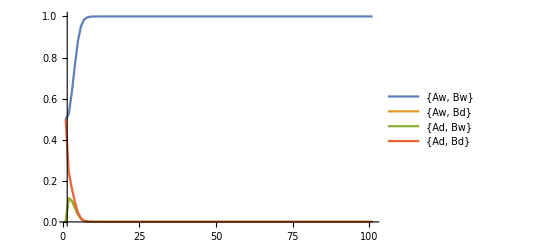

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

```mathematica
fun[s_,r_,Finit_]:=Block[{Loci,Gametes,Genotypes,pars,FitnessPayload,FitnessToxin,Fitness,t,F},
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
FitnessPayload=MakeFitnessMatrix[{"Ad","Bd"},pars,s];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"recombination"->r|>;

F[0]={1-Finit,0,0,Finit};
F[1]=Recombination[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars];

]
```

## Unstable equilibrium analysis

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
FitnessPayload=MakeFitnessMatrix[{"Ad","Bd"},pars,s];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,ϵ];
Fitness=FitnessPayload*FitnessToxin;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"recombination"->r|>;

Clear[F]
eq=Recombination[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars]//Simplify;
```

```mathematica
neweq=FullSimplify[eq[[{1,4}]]/.F[2]->1/2(1-F[1]-F[4])/.F[3]->1/2(1-F[1]-F[4])];
```

```mathematica
sol=Solve[neweq=={F[1],F[4]},{F[1],F[4]}]
```

{{F[1]→1,F[4]→0},{F[1]→0,F[4]→1},3,{1,1},{F[1]→(-28298656+182188544 s-599620536 s^2+357+36904 s^36 Root[1&,5]^6-980 s^37 Root[1&,5]^6)/(-28298656+182188544 s-599620536 s^2+1306765552 s^3-2109155936 s^4+26+6033538 s^23-1249563 s^24+188136 s^25-19407 s^26+1218 s^27-35 s^28),F[4]→Root[1+6+1+(-208+19) #1^5&,5]}}
 |  |  |  |

```mathematica
(*COOL! First root is unstable equilibrium, second root is stable equilibrium!
Can check with: F[1]=0.5466052543488716 ,F[2]=F[3]=0.12206347842681585,F[4]=0.20926778879749666 (s=.053, r=0.5,ϵ=1). It goes to 0.9016066889113552
*)
```

```mathematica
Manipulate[Plot[-r^3 s^2-2 r^2 s^3+2 r^3 s^3+r^2 s^4-r^3 s^4-2 r^3 s ϵ-4 r^2 s^2 ϵ+6 r^3 s^2 ϵ+6 r^2 s^3 ϵ-6 r^3 s^3 ϵ-2 r^2 s^4 ϵ+2 r^3 s^4 ϵ-r^3 ϵ^2-2 r^2 s ϵ^2+4 r^3 s ϵ^2+5 r^2 s^2 ϵ^2-6 r^3 s^2 ϵ^2-4 r^2 s^3 ϵ^2+4 r^3 s^3 ϵ^2+r^2 s^4 ϵ^2-r^3 s^4 ϵ^2+(8 r s^4-6 r^2 s^4+3 r^3 s^4-4 r s^5+10 r^2 s^5-6 r^3 s^5-3 r^2 s^6+3 r^3 s^6-12 r^3 s ϵ-22 r^2 s^2 ϵ+60 r^3 s^2 ϵ+12 r s^3 ϵ+74 r^2 s^3 ϵ-108 r^3 s^3 ϵ-6 r s^4 ϵ-76 r^2 s^4 ϵ+84 r^3 s^4 ϵ-4 r s^5 ϵ+26 r^2 s^5 ϵ-24 r^3 s^5 ϵ+2 r s^6 ϵ-2 r^2 s^6 ϵ+13 r^3 ϵ^2+30 r^2 s ϵ^2-48 r^3 s ϵ^2+24 r s^2 ϵ^2-76 r^2 s^2 ϵ^2+63 r^3 s^2 ϵ^2-50 r s^3 ϵ^2+58 r^2 s^3 ϵ^2-32 r^3 s^3 ϵ^2+23 r s^4 ϵ^2-7 r^2 s^4 ϵ^2+3 r^3 s^4 ϵ^2-6 r^2 s^5 ϵ^2-r s^6 ϵ^2+r^2 s^6 ϵ^2+r^3 s^6 ϵ^2-8 r^2 ϵ^3-16 r s ϵ^3+24 r^2 s ϵ^3+24 r s^2 ϵ^3-24 r^2 s^2 ϵ^3-8 r s^3 ϵ^3+8 r^2 s^3 ϵ^3) x+(-24 r s^6+17 r^2 s^6-3 r^3 s^6+12 r s^7-18 r^2 s^7+6 r^3 s^7+3 r^2 s^8-3 r^3 s^8+4 r^2 s^2 ϵ+12 r^3 s^2 ϵ+88 r s^3 ϵ-68 r^2 s^3 ϵ-60 r^3 s^3 ϵ-312 r s^4 ϵ+168 r^2 s^4 ϵ+100 r^3 s^4 ϵ-64 s^5 ϵ+310 r s^5 ϵ-138 r^2 s^5 ϵ-58 r^3 s^5 ϵ+48 s^6 ϵ-80 r s^6 ϵ+26 r^2 s^6 ϵ-6 r^3 s^6 ϵ-8 s^7 ϵ-6 r s^7 ϵ+6 r^2 s^7 ϵ+14 r^3 s^7 ϵ+2 r^2 s^8 ϵ-2 r^3 s^8 ϵ-16 r^3 ϵ^2-88 r^2 s ϵ^2+52 r^3 s ϵ^2-112 r s^2 ϵ^2+307 r^2 s^2 ϵ^2-53 r^3 s^2 ϵ^2-96 s^3 ϵ^2+266 r s^3 ϵ^2-366 r^2 s^3 ϵ^2+12 r^3 s^3 ϵ^2+200 s^4 ϵ^2-139 r s^4 ϵ^2+153 r^2 s^4 ϵ^2+2 r^3 s^4 ϵ^2-68 s^5 ϵ^2-46 r s^5 ϵ^2-2 r^2 s^5 ϵ^2+8 r^3 s^5 ϵ^2-12 s^6 ϵ^2+33 r s^6 ϵ^2-5 r^3 s^6 ϵ^2+4 s^7 ϵ^2+2 r s^7 ϵ^2-2 r^2 s^7 ϵ^2-2 r^2 s^8 ϵ^2+46 r^2 ϵ^3+76 r s ϵ^3-144 r^2 s ϵ^3+96 s^2 ϵ^3-164 r s^2 ϵ^3+150 r^2 s^2 ϵ^3-140 s^3 ϵ^3+84 r s^3 ϵ^3-48 r^2 s^3 ϵ^3+22 s^4 ϵ^3+28 r s^4 ϵ^3-6 r^2 s^4 ϵ^3+16 s^5 ϵ^3-24 r s^5 ϵ^3-2 s^6 ϵ^3+2 r^2 s^6 ϵ^3-12 r ϵ^4-24 s ϵ^4+32 r s ϵ^4+28 s^2 ϵ^4-24 r s^2 ϵ^4-4 s^4 ϵ^4+4 r s^4 ϵ^4) x^2+(24 r s^8-15 r^2 s^8+r^3 s^8-12 r s^9+14 r^2 s^9-2 r^3 s^9-r^2 s^10+r^3 s^10-64 r s^4 ϵ+66 r^2 s^4 ϵ+4 r^3 s^4 ϵ+280 r s^5 ϵ-188 r^2 s^5 ϵ-8 r^3 s^5 ϵ+256 s^6 ϵ-404 r s^6 ϵ+124 r^2 s^6 ϵ-240 s^7 ϵ+168 r s^7 ϵ+46 r^2 s^7 ϵ+8 r^3 s^7 ϵ+56 s^8 ϵ-2 r s^8 ϵ-44 r^2 s^8 ϵ-4 r^3 s^8 ϵ-6 r^2 s^9 ϵ-2 r s^10 ϵ+2 r^2 s^10 ϵ+4 r^3 ϵ^2-8 r^3 s ϵ^2+256 r s^2 ϵ^2+4 r^2 s^2 ϵ^2-4 r^3 s^2 ϵ^2-776 r s^3 ϵ^2-84 r^2 s^3 ϵ^2+16 r^3 s^3 ϵ^2+320 s^4 ϵ^2+636 r s^4 ϵ^2+181 r^2 s^4 ϵ^2-4 r^3 s^4 ϵ^2-768 s^5 ϵ^2-18 r s^5 ϵ^2-84 r^2 s^5 ϵ^2-8 r^3 s^5 ϵ^2+368 s^6 ϵ^2-48 r s^6 ϵ^2-53 r^2 s^6 ϵ^2+4 r^3 s^6 ϵ^2+24 s^7 ϵ^2-34 r s^7 ϵ^2+30 r^2 s^7 ϵ^2-28 s^8 ϵ^2-11 r s^8 ϵ^2+6 r^2 s^8 ϵ^2+6 r s^9 ϵ^2+r s^10 ϵ^2-30 r^2 ϵ^3-260 r s ϵ^3+112 r^2 s ϵ^3-96 s^2 ϵ^3+724 r s^2 ϵ^3-134 r^2 s^2 ϵ^3-132 s^3 ϵ^3-532 r s^3 ϵ^3+40 r^2 s^3 ϵ^3+458 s^4 ϵ^3-28 r s^4 ϵ^3+14 r^2 s^4 ϵ^3-188 s^5 ϵ^3+76 r s^5 ϵ^3+8 r^2 s^5 ϵ^3-38 s^6 ϵ^3+20 r s^6 ϵ^3-10 r^2 s^6 ϵ^3+20 s^7 ϵ^3+4 r s^7 ϵ^3-4 r s^8 ϵ^3+72 r ϵ^4+48 s ϵ^4-192 r s ϵ^4-8 s^2 ϵ^4+144 r s^2 ϵ^4-80 s^3 ϵ^4+36 s^4 ϵ^4-24 r s^4 ϵ^4+8 s^5 ϵ^4-4 s^6 ϵ^4) x^3+(-8 r s^10+3 r^2 s^10+4 r s^11-4 r^2 s^11-80 r s^6 ϵ+20 r^2 s^6 ϵ-320 s^7 ϵ+352 r s^7 ϵ-32 r^2 s^7 ϵ+320 s^8 ϵ-284 r s^8 ϵ-8 r^2 s^8 ϵ-48 s^9 ϵ+14 r s^9 ϵ+18 r^2 s^9 ϵ-32 s^10 ϵ+36 r s^10 ϵ+2 r^2 s^10 ϵ+8 s^11 ϵ-6 r s^11 ϵ+28 r^2 s^2 ϵ^2-272 r s^3 ϵ^2-48 r^2 s^3 ϵ^2+1016 r s^4 ϵ^2-40 r^2 s^4 ϵ^2-288 s^5 ϵ^2-1024 r s^5 ϵ^2+72 r^2 s^5 ϵ^2+752 s^6 ϵ^2+16 r s^6 ϵ^2+16 r^2 s^6 ϵ^2-320 s^7 ϵ^2+256 r s^7 ϵ^2-16 r^2 s^7 ϵ^2-144 s^8 ϵ^2+15 r s^8 ϵ^2-12 r^2 s^8 ϵ^2+84 s^9 ϵ^2-22 r s^9 ϵ^2+4 s^10 ϵ^2-5 r s^10 ϵ^2-4 s^11 ϵ^2-16 r^2 ϵ^3+200 r s ϵ^3+8 r^2 s ϵ^3-456 r s^2 ϵ^3+32 r^2 s^2 ϵ^3+272 s^3 ϵ^3+40 r s^3 ϵ^3-320 s^4 ϵ^3+352 r s^4 ϵ^3-32 r^2 s^4 ϵ^3-116 s^5 ϵ^3-20 r s^5 ϵ^3-8 r^2 s^5 ϵ^3+120 s^6 ϵ^3-124 r s^6 ϵ^3+16 r^2 s^6 ϵ^3+52 s^7 ϵ^3-4 r s^7 ϵ^3-30 s^8 ϵ^3+12 r s^8 ϵ^3-4 s^9 ϵ^3+2 s^10 ϵ^3-108 r ϵ^4-24 s ϵ^4+288 r s ϵ^4-68 s^2 ϵ^4-216 r s^2 ϵ^4+160 s^3 ϵ^4-60 s^4 ϵ^4+36 r s^4 ϵ^4-16 s^5 ϵ^4+8 s^6 ϵ^4) x^4+(r^2 s^12+128 s^8 ϵ-96 r s^8 ϵ+6 r^2 s^8 ϵ-128 s^9 ϵ+96 r s^9 ϵ+8 r s^10 ϵ-6 r^2 s^10 ϵ+32 s^11 ϵ-24 r s^11 ϵ-8 s^12 ϵ+4 r s^12 ϵ+64 r s^4 ϵ^2+12 r^2 s^4 ϵ^2-320 r s^5 ϵ^2+64 s^6 ϵ^2+400 r s^6 ϵ^2-24 r^2 s^6 ϵ^2-192 s^7 ϵ^2-32 r s^7 ϵ^2+48 s^8 ϵ^2-132 r s^8 ϵ^2+12 r^2 s^8 ϵ^2+96 s^9 ϵ^2+16 r s^9 ϵ^2-40 s^10 ϵ^2+12 r s^10 ϵ^2-8 s^11 ϵ^2+4 s^12 ϵ^2+8 r^2 ϵ^3-128 r s^2 ϵ^3-24 r^2 s^2 ϵ^3+416 r s^3 ϵ^3-160 s^4 ϵ^3-352 r s^4 ϵ^3+24 r^2 s^4 ϵ^3+288 s^5 ϵ^3-32 r s^5 ϵ^3-80 s^6 ϵ^3+104 r s^6 ϵ^3-8 r^2 s^6 ϵ^3-72 s^7 ϵ^3+30 s^8 ϵ^3-8 r s^8 ϵ^3+4 s^9 ϵ^3-2 s^10 ϵ^3+48 r ϵ^4-128 r s ϵ^4+48 s^2 ϵ^4+96 r s^2 ϵ^4-80 s^3 ϵ^4+28 s^4 ϵ^4-16 r s^4 ϵ^4+8 s^5 ϵ^4-4 s^6 ϵ^4)x^5,{x,0,1}],{s,0,1},{ϵ,0,1},{r,0,0.5}]
```

Unstable equilibrium analysis

```mathematica
neweq1=neweq/.r->1/2/.ϵ->1;
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}];
```

```mathematica
res11=Table[{s1,Select[{F[4],1-F[1]}/.sol/.r->1/2/.s->s1/.ϵ->1,(0<Re[#[[1]]]<1&&0<=Im[#[[1]]]<10^-12)&][[1]]},{s1,0.00001,0.27760984,0.005}];
res12=Table[{s1,Select[F[4]/.sol/.r->1/2/.s->s1/.ϵ->1,(0<Re[#]<1&&0<=Im[#]<10^-12)&][[2]]},{s1,0.00001,0.27760984,0.005}];
```

```mathematica
test1=ListLinePlot[res12,AxesLabel->{"s","Freq F[4]"},PlotRange->{Automatic,{0,1}}];
```

```mathematica
test2=ListLinePlot[{Transpose[{res11[[;;,1]],res11[[;;,2,1]]}],Transpose[{res11[[;;,1]],res11[[;;,2,2]]}]},Filling->{1->{2}},PlotStyle->{Orange}];
```

```mathematica
p1=Show[{test1,test2}];
```

```mathematica
neweq1=neweq/.r->1/2/.ϵ->3/4;
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}];
```

```mathematica
res11=Table[{s1,Select[{F[4],1-F[1]}/.sol/.r->1/2/.s->s1,(0<Re[#[[1]]]<1&&0<=Im[#[[1]]]<10^-12)&][[1]]},{s1,0.00001,0.210,0.005}];
res12=Table[{s1,Select[F[4]/.sol/.r->1/2/.s->s1/.ϵ->1,(0<Re[#]<1&&0<=Im[#]<10^-12)&][[2]]},{s1,0.00001,0.210,0.005}];
```

```mathematica
test1=ListLinePlot[res12,AxesLabel->{"s","Freq F[4]"},PlotRange->{Automatic,{0,1}},PlotStyle->{Dashing[Large]}];
```

```mathematica
test2=ListLinePlot[{Transpose[{res11[[;;,1]],res11[[;;,2,1]]}],Transpose[{res11[[;;,1]],res11[[;;,2,2]]}]},Filling->{1->{2}},PlotStyle->{{Orange,Dashing[Large]}}];
```

```mathematica
p2=Show[{test1,test2}];
```

```mathematica
neweq1=neweq/.r->1/2/.ϵ->1/2;
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}];
```

```mathematica
res11=Table[{s1,Select[{F[4],1-F[1]}/.sol/.r->1/2/.s->s1,(0<Re[#[[1]]]<1&&0<=Im[#[[1]]]<10^-12)&][[1]]},{s1,0.00001,0.140,0.005}];
res12=Table[{s1,Select[F[4]/.sol/.r->1/2/.s->s1/.ϵ->1,(0<Re[#]<1&&0<=Im[#]<10^-12)&][[2]]},{s1,0.00001,0.140,0.005}];
```

```mathematica
test1=ListLinePlot[res12,AxesLabel->{"s","Freq F[4]"},PlotRange->{Automatic,{0,1}},PlotStyle->{Dashed}];
```

```mathematica
test2=ListLinePlot[{Transpose[{res11[[;;,1]],res11[[;;,2,1]]}],Transpose[{res11[[;;,1]],res11[[;;,2,2]]}]},Filling->{1->{2}},PlotStyle->{{Orange,Dashed}}];
```

```mathematica
p3=Show[{test1,test2}];
```

```mathematica
neweq1=neweq/.r->1/2/.ϵ->1/4;
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}];
```

```mathematica
res11=Table[{s1,Select[{F[4],1-F[1]}/.sol/.r->1/2/.s->s1,(0<Re[#[[1]]]<1&&0<=Im[#[[1]]]<10^-12)&][[1]]},{s1,0.00001,0.0685,0.0005}];
res12=Table[{s1,Select[F[4]/.sol/.r->1/2/.s->s1/.ϵ->1,(0<Re[#]<1&&0<=Im[#]<10^-12)&][[2]]},{s1,0.00001,0.0685,0.0005}];
```

```mathematica
test1=ListLinePlot[res12,AxesLabel->{"s","Freq F[4]"},PlotRange->{Automatic,{0,1}},PlotStyle->{Dotted}];
```

```mathematica
test2=ListLinePlot[{Transpose[{res11[[;;,1]],res11[[;;,2,1]]}],Transpose[{res11[[;;,1]],res11[[;;,2,2]]}]},Filling->{1->{2}},PlotStyle->{{Orange,Dotted}}];
```

```mathematica
p4=Show[{test1,test2}];
```

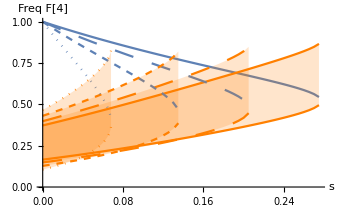

```mathematica
Show[p1,p2,p3,p4]
```

## 2 locus EUD w/ Dominance

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
FitnessPayload=MakeDominantPayloadMatrix[{"Ad","Bd"},pars,0.9];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"recombination"->0.5|>;
```

```mathematica
Clear[F];
F[0]={0.001,0.0,0.0,0.999};
F[t_]:=F[t]=Recombination[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars]
```

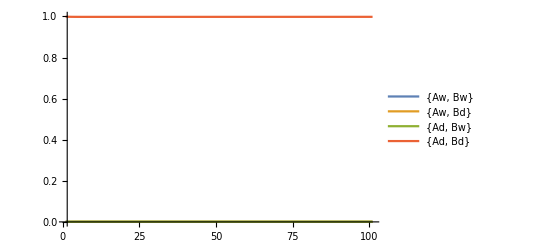

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

## Unstable equilibrium analysis

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
FitnessPayload=MakeDominantPayloadMatrix[{"Ad","Bd"},pars,s];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,ϵ];
Fitness=FitnessPayload*FitnessToxin;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"recombination"->r|>;

Clear[F]
eq=Recombination[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars]//Simplify;
```

```mathematica
neweq=FullSimplify[eq[[{1,4}]]/.F[2]->1/2(1-F[1]-F[4])/.F[3]->1/2(1-F[1]-F[4])];
```

```mathematica
neweq1=neweq/.r->1/2/.ϵ->1;
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}];
```

```mathematica
plot1=Plot[{F[4]/.sol[[6]],1-F[1]/.sol[[6]]},{s,0,0.9999},WorkingPrecision->50,Filling->{1->{2}},AxesLabel->{"s","Freq F[4]"},PlotStyle->{{Orange}},PlotRange->{{0,1},{0,1}}];
```

```mathematica
neweq1=neweq/.r->1/2/.ϵ->3/4;
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}];
```

```mathematica
plot2=Plot[{F[4]/.sol[[6]],1-F[1]/.sol[[6]]},{s,0,0.9999},WorkingPrecision->50,Filling->{1->{2}},AxesLabel->{"s","Freq F[4]"},PlotStyle->{{Orange,Dashing[Large]}},PlotRange->{{0,1},{0,1}}];
```

```mathematica
neweq1=neweq/.r->1/2/.ϵ->1/2;
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}];
```

```mathematica
plot3=Plot[{F[4]/.sol[[6]],1-F[1]/.sol[[6]]},{s,0,0.9999},WorkingPrecision->50,Filling->{1->{2}},AxesLabel->{"s","Freq F[4]"},PlotRange->{{0,1},{0,1}},PlotStyle->{{Orange,Dashed}}];
```

```mathematica
neweq1=neweq/.r->1/2/.ϵ->1/4;
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}];
```

```mathematica
plot4=Plot[{F[4]/.sol[[6]],1-F[1]/.sol[[6]]},{s,0,0.9999},WorkingPrecision->50,Filling->{1->{2}},AxesLabel->{"s","Freq F[4]"},PlotRange->{Automatic,{0,1}},PlotStyle->{{Orange,Dotted}}];
```

```mathematica
absorb1=ListLinePlot[{{0,1},{1,1}},AxesLabel->{"s","Freq F[4]"},PlotRange->{Automatic,{0,1}}];
```

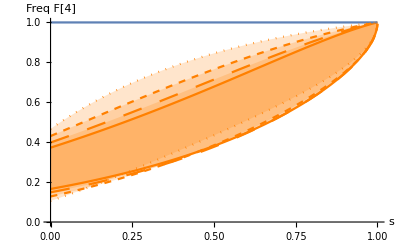

```mathematica
Show[{plot1,plot2,plot3,plot4,absorb1}]
```

## 2 locus EUD w/ Recessive

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
FitnessPayload=MakeRecessivePayloadMatrix[{"Ad","Bd"},pars,0.1];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"recombination"->0.5|>;
```

```mathematica
Clear[F];
F[0]={0.7,0.0,0.0,0.3};
F[t_]:=F[t]=Recombination[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars]
```

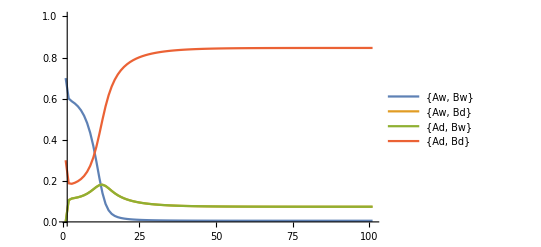

```mathematica
ListLinePlot[Transpose[Table[F[t],{t,0,100}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

## Unstable equilibrium analysis

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
FitnessPayload=MakeRecessivePayloadMatrix[{"Ad","Bd"},pars,s];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Ad","Bd"},pars,ϵ];
Fitness=FitnessPayload*FitnessToxin;
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"recombination"->r|>;

Clear[F]
eq=Recombination[DiploidSelection[ConvertToGenotypes[Table[F[i],{i,1,Length[Gametes]}],pars],pars],pars]//Simplify;
```

```mathematica
neweq=FullSimplify[eq[[{1,4}]]/.F[2]->1/2(1-F[1]-F[4])/.F[3]->1/2(1-F[1]-F[4])];
```

```mathematica
neweq1=neweq/.r->1/2/.ϵ->1;
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}];
```

```mathematica
plot11=Plot[{F[4]/.sol[[3]],1-F[1]/.sol[[3]]},{s,0,0.9999},WorkingPrecision->50,Filling->{1->{2}},AxesLabel->{"s","Freq F[4]"},PlotStyle->{{Orange}},PlotRange->{{0,1},{0,1}}];
```

```mathematica
plot12=Plot[{F[4]/.sol[[4]]},{s,0,0.9999},WorkingPrecision->50,AxesLabel->{"s","Freq F[4]"},PlotRange->{{0,1},{0,1}}];
```

```mathematica
plot1=Show[{plot11,plot12}];
```

```mathematica
neweq1=neweq/.r->1/2/.ϵ->3/4;
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}];
```

```mathematica
plot21=Plot[{F[4]/.sol[[3]],1-F[1]/.sol[[3]]},{s,0,0.9999},WorkingPrecision->50,Filling->{1->{2}},AxesLabel->{"s","Freq F[4]"},PlotStyle->{{Orange,Dashing[Large]}},PlotRange->{{0,1},{0,1}}];
plot22=Plot[{F[4]/.sol[[4]]},{s,0,0.9999},WorkingPrecision->50,AxesLabel->{"s","Freq F[4]"},PlotRange->{{0,1},{0,1}},PlotStyle->{{Dashing[Large]}}];
```

```mathematica
plot2=Show[{plot21,plot22}];
```

```mathematica
neweq1=neweq/.r->1/2/.ϵ->1/2;
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}];
```

```mathematica
plot31=Plot[{F[4]/.sol[[3]],1-F[1]/.sol[[3]]},{s,0,0.9999},WorkingPrecision->50,Filling->{1->{2}},AxesLabel->{"s","Freq F[4]"},PlotStyle->{{Orange,Dashed}},PlotRange->{{0,1},{0,1}}];
plot32=Plot[{F[4]/.sol[[4]]},{s,0,0.9999},WorkingPrecision->50,AxesLabel->{"s","Freq F[4]"},PlotRange->{{0,1},{0,1}},PlotStyle->{{Dashed}}];
```

```mathematica
plot3=Show[{plot31,plot32}];
```

```mathematica
neweq1=neweq/.r->1/2/.ϵ->1/4;
sol=Solve[neweq1=={F[1],F[4]},{F[1],F[4]}];
```

```mathematica
plot41=Plot[{F[4]/.sol[[3]],1-F[1]/.sol[[3]]},{s,0,0.58},WorkingPrecision->50,Filling->{1->{2}},AxesLabel->{"s","Freq F[4]"},PlotStyle->{{Orange,Dotted}},PlotRange->{{0,1},{0,1}}];
plot42=Plot[{F[4]/.sol[[4]]},{s,0,0.58},WorkingPrecision->50,AxesLabel->{"s","Freq F[4]"},PlotRange->{{0,1},{0,1}},PlotStyle->{{Dotted}}];
```

```mathematica
plot4=Show[{plot41,plot42}];
```

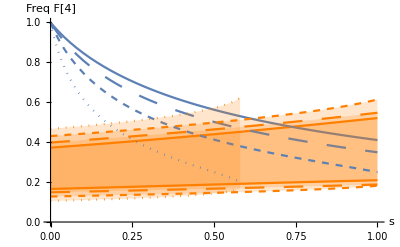

```mathematica
Show[{plot1,plot2,plot3,plot4}]
```

## Daisy chain 2 loci, varying s

```mathematica
fun2loci[f40_,s_,r_,d_]:=fun2loci[f40,s,r,d]=Block[{F1,F4,t},
On[Assert];
F1[0]=1-f40;
F4[0]=f40;
F1[1]=(F1[0] (1-s+s F1[0]+(-1+s) (r+d (-1+r) (-1+s)+s-r s) F4[0]))/(1+s (-1+F1[0]+(-1+s) F4[0]))^2;  
F4[1]=((-1+s)^2 F4[0] (1+(-1+d) r F1[0]+s (-1+F1[0]+(-1+s) F4[0])))/(1+s (-1+F1[0]+(-1+s) F4[0]))^2; 
Assert[F1[1]<F1[0]];
t=0;
While[F1[t+1]<F1[t],
t+=1;
F1[t+1]=(F1[t] (1-s+s F1[t]+(-1+s) (r+d (-1+r) (-1+s)+s-r s) F4[t]))/(1+s (-1+F1[t]+(-1+s) F4[t]))^2;
F4[t+1]=((-1+s)^2 F4[t] (1+(-1+d) r F1[t]+s (-1+F1[t]+(-1+s) F4[t])))/(1+s (-1+F1[t]+(-1+s) F4[t]))^2;
];
{F1[t],F4[t],t}
]
```

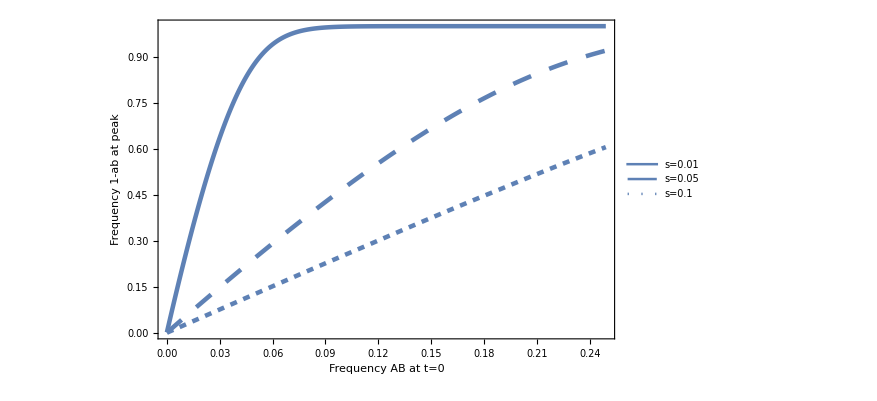

```mathematica
plot1=ListLinePlot[Table[{f,1-fun2loci[f,0.01,0.5,1][[1]]},{f,0.00005,0.25,0.001}],PlotStyle->{Thickness[0.005]},PlotRange->All,AxesLabel->{"F[4] init","1-F[1] max"}];
plot2=ListLinePlot[Table[{f,1-fun2loci[f,0.05,0.5,1][[1]]},{f,0.00005,0.25,0.001}],PlotStyle->{Thickness[0.005],Dashing[Large],CapForm["Round"]},PlotRange->All];
plot3=ListLinePlot[Table[{f,1-fun2loci[f,0.1,0.5,1][[1]]},{f,0.00005,0.25,0.001}],PlotStyle->{Thickness[0.005],Dashed,CapForm["Round"]},PlotRange->All];

Legended[Show[{plot1,plot2,plot3},
Frame->True, 
FrameLabel->{Style["Frequency AB at t=0",LabelSize],Style["Frequency 1-ab at peak",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False],
Placed[
LineLegend[{
Directive[Darker[Black],Thickness[0.01],ColorData[97,"ColorList"][[1]]],
Directive[Darker[Black],Thickness[0.01],ColorData[97,"ColorList"][[1]],Dashing[Large],CapForm["Round"]],
Directive[Darker[Black],Thickness[0.01],ColorData[97,"ColorList"][[1]],Dotted,CapForm["Round"]]
},
{
Style["s=0.01",LabelSize],
Style["s=0.05",LabelSize],
Style["s=0.1",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.85,0.2}
]
]
```

## Daisy chain n loci, varying n

```mathematica
funNloci[f40_,n_,s_,r_,d_]:=funNloci[f40,n,s,r,d]=Block[{F,F0,t,Loci,Gametes,Genotypes,pars,Fitness,DriveMatrix},
Loci=Table[{ToString[nid]<>"w",ToString[nid]<>"d"},{nid,1,n}];
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
Fitness=MakeFitnessMatrix[Loci[[;;,2]],pars,s];
DriveMatrix=MakeDriveMatrix[Table[{Loci[[i,2]],Loci[[i+1,1]]},{i,1,Length[Loci]-1}],pars,d];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->r|>;
F0=Table[0,{i,1,Length[Gametes]}];
F0[[1]]=1-f40;
F0[[Length[Gametes]]]=f40;
F[0]=F0;
F[t_]:=F[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars],pars];

On[Assert];
Assert[F[1][[1]]<F[0][[1]]];
t=0;
While[F[t+1][[1]]<F[t][[1]],t+=1];
{1-F[t][[1]],t}
]
```

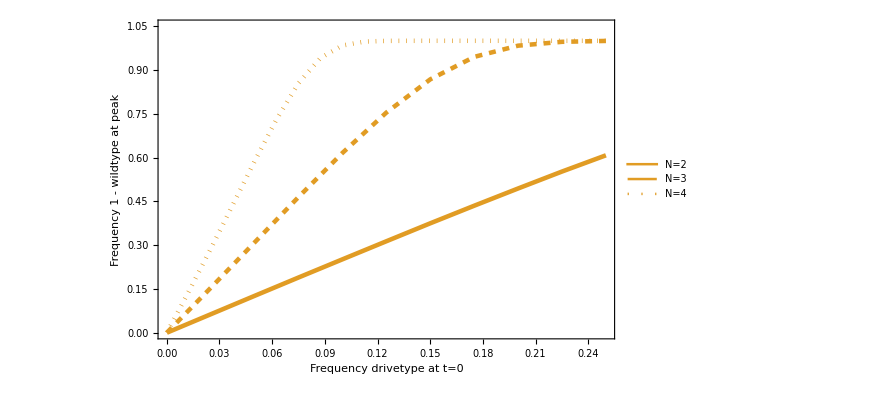

```mathematica
plot1=ListLinePlot[Table[{f,funNloci[f,2,0.1,0.5,1][[1]]},{f,0.00005,0.26,0.025}],PlotStyle->{{Thickness[0.005],ColorData[97,"ColorList"][[2]]}},PlotRange->{{0,0.25},{0,1.05}}];
plot2=ListLinePlot[Table[{f,funNloci[f,3,0.1,0.5,1][[1]]},{f,0.00005,0.26,0.025}],PlotRange->All,PlotStyle->{{ColorData[97,"ColorList"][[2]],Thickness[0.005], Dashed}}];
plot3=ListLinePlot[Table[{f,funNloci[f,4,0.1,0.5,1][[1]]},{f,0.00005,0.26,0.0125}],PlotRange->All,PlotStyle->{{ColorData[97,"ColorList"][[2]],Thickness[0.005],Dotted}}];
Legended[Show[{plot1,plot2,plot3},
Frame->True, 
FrameLabel->{Style["Frequency drivetype at t=0",LabelSize],Style["Frequency 1 - wildtype at peak",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False],
Placed[
LineLegend[{
Directive[Darker[Black],Thickness[0.01],ColorData[97,"ColorList"][[2]]],
Directive[Darker[Black],Thickness[0.01],ColorData[97,"ColorList"][[2]],Dashing[Large],CapForm["Round"]],
Directive[Darker[Black],Thickness[0.01],ColorData[97,"ColorList"][[2]],Dotted,CapForm["Round"]]
},
{
Style["N=2",LabelSize],
Style["N=3",LabelSize],
Style["N=4",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.85,0.2}
]
]
```

## TestCase 1

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeFitnessMatrix[{"Ad","Bd","Cd","Dd"},pars,0.1];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Cd","Dd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Bd","Dw"},{"Bd","Cw"}},pars,1];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->1/2|>;
```

```mathematica
Clear[F];
F[0]={0.9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.1};
F[t_]:=F[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars],pars]
```

```mathematica
plot1=ListLinePlot[Transpose[Table[F[t],{t,0,100}]][[{1,4},;;]],PlotRange->{Automatic,{0,1.01}},AxesLabel->{"t","Freq"}];
```

```mathematica
Clear[F2];
F2[0]={0.975,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.025};
F2[t_]:=F2[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F2[t-1],pars],pars],pars],pars]
```

```mathematica
plot2=ListLinePlot[Transpose[Table[F2[t],{t,0,100}]][[{1,4},;;]],PlotStyle->Dashed];
```

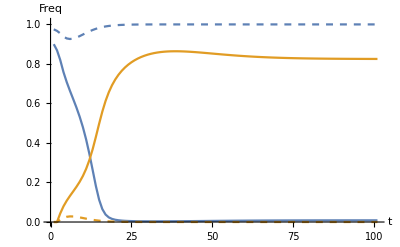

```mathematica
showdyn=Show[plot1,plot2]
```

```mathematica
load1=ListLinePlot[Table[1-ConvertToGenotypes[F[t],pars].Fitness,{t,0,100}],PlotRange->{Automatic,{0,0.5}},AxesLabel->{"t","Load"},PlotStyle->Black];
load2=ListLinePlot[Table[1-ConvertToGenotypes[F2[t],pars].Fitness,{t,0,100}],PlotRange->{Automatic,{0,1}},PlotStyle->{Dashed,Black}];
```

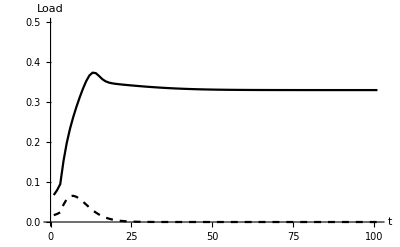

```mathematica
showload=Show[load1,load2]
```

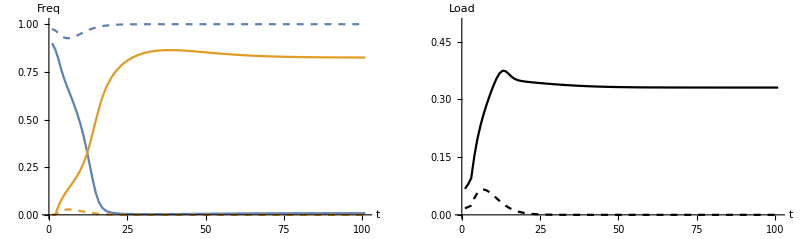

```mathematica
GraphicsGrid[{{showdyn,showload}},PlotLabel->"Multiplicative payload, 4Loci, s=0.1,d=1,ϵ=1,r=0.5"]
```

```mathematica
Export["C:\\Users\\Freek\\Documents\\GeneDrive\\Figures\\Example4Loci1.pdf",%959,"PDF"]
```

C:\Users\Freek\Documents\GeneDrive\Figures\Example4Loci1.pdf

## TestCase 1a - Migration

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeFitnessMatrix[{"Ad","Bd","Cd","Dd"},pars,0.1];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Cd","Dd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Bd","Dw"},{"Bd","Cw"}},pars,1];
pars1=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->1/2|>;
```

```mathematica
Clear[F11,F21,F31];
F11[0]={0.9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.1};
F21[0]={1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
F31[0]={1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

m=0.01;
F11[t_]:=F11[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F11[t-1],pars1],pars1],pars1],pars1]
F21[t_]:=F21[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F21[t-1]-m(F21[t-1]-F11[t-1]),pars1],pars1],pars1],pars1]
F31[t_]:=F31[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F31[t-1]-m(F31[t-1]-F21[t-1]),pars1],pars1],pars1],pars1]
```

```mathematica
P11=ListLinePlot[Transpose[Table[F11[t],{t,0,50}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}},PlotLabel->"Population 1"];
P21=ListLinePlot[Transpose[Table[F21[t],{t,0,50}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}},PlotLabel->"Population 2"];
P31=ListLinePlot[Transpose[Table[F31[t],{t,0,50}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}},PlotLabel->"Population 3"];
```

```mathematica
Clear[F12,F22,F32];
F12[0]={0.9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.1};
F22[0]={1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
F32[0]={1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

m=0.05;
F12[t_]:=F12[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F12[t-1],pars1],pars1],pars1],pars1]
F22[t_]:=F22[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F22[t-1]-m(F22[t-1]-F12[t-1]),pars1],pars1],pars1],pars1]
F32[t_]:=F32[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F32[t-1]-m(F32[t-1]-F22[t-1]),pars1],pars1],pars1],pars1]
```

```mathematica
P12=ListLinePlot[Transpose[Table[F12[t],{t,0,50}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
P22=ListLinePlot[Transpose[Table[F22[t],{t,0,50}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
P32=ListLinePlot[Transpose[Table[F32[t],{t,0,50}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
```

```mathematica
Clear[F13,F23,F33];
F13[0]={0.9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.1};
F23[0]={1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
F33[0]={1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

m=0.1;
F13[t_]:=F13[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F13[t-1],pars1],pars1],pars1],pars1]
F23[t_]:=F23[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F23[t-1]-m(F23[t-1]-F13[t-1]),pars1],pars1],pars1],pars1]
F33[t_]:=F33[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F33[t-1]-m(F33[t-1]-F23[t-1]),pars1],pars1],pars1],pars1]
```

```mathematica
P13=ListLinePlot[Transpose[Table[F13[t],{t,0,50}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
P23=ListLinePlot[Transpose[Table[F23[t],{t,0,50}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
P33=ListLinePlot[Transpose[Table[F33[t],{t,0,50}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
```

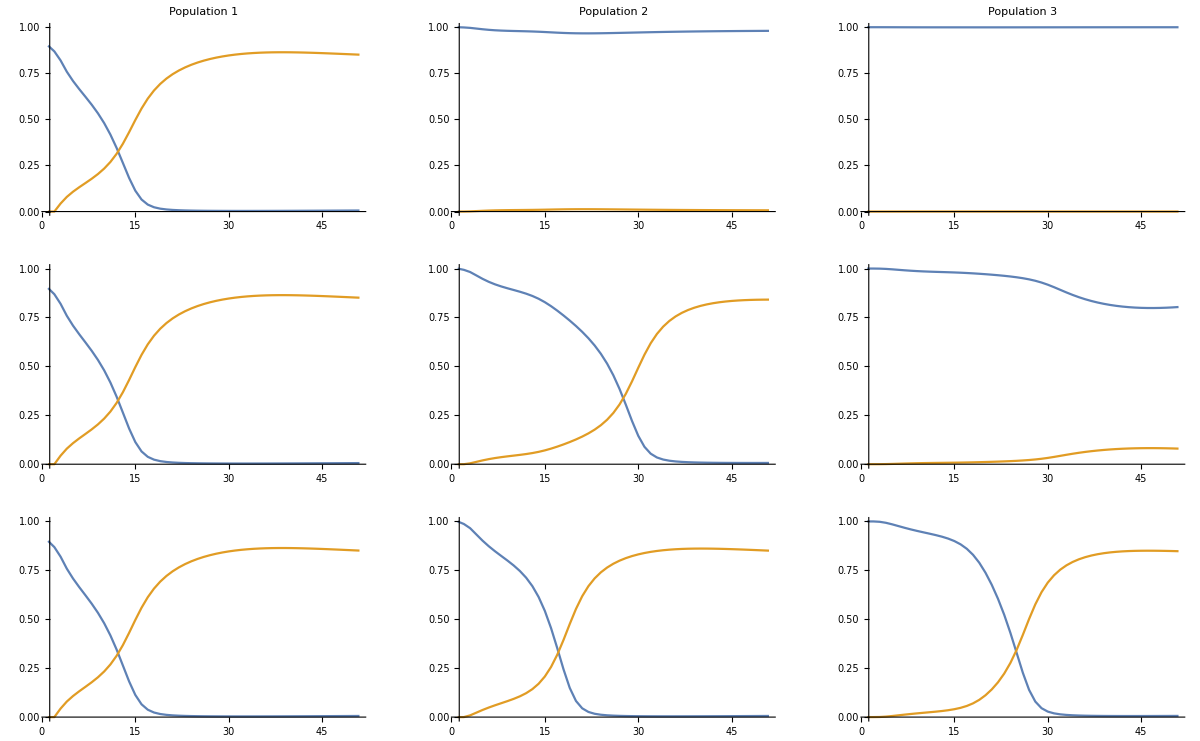

```mathematica
GraphicsGrid[{{P11,P21,P31},{P12,P22,P32},{P13,P23,P33}},PlotLabel->"m=0.01, m=0.05,m=0.1"]
```

```mathematica
Export["C:\\Users\\Freek\\Documents\\GeneDrive\\Figures\\Test.pdf",%936,"PDF"]
```

C:\Users\Freek\Documents\GeneDrive\Figures\Test.pdf

```mathematica
Export["C:\\Users\\Freek\\Documents\\GeneDrive\\Figures\\ExampleMigration.pdf",%925,"PDF"]
```

C:\Users\Freek\Documents\GeneDrive\Figures\ExampleMigration.pdf

## From EUD to invasion = hard?

At s=0.1, you need 0.2 minimum replaced right? does not look like it. What’s going on....

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeFitnessMatrix[{"Ad","Bd","Cd","Dd"},pars,0.1];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Cd","Dd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Bd","Dw"},{"Bd","Cw"}},pars,1];
pars1=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->1/2|>;
```

```mathematica
Clear[F1,F2];
F1[0]={0.9,0,0,0.1,0,0,0,0,0,0,0,0,0,0,0,0.0};
```

```mathematica
F1[t_]:=F1[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F1[t-1],pars1],pars1],pars1],pars1]
```

```mathematica
F1[100]
```

{0.00855153,0.0831001,0.0831001,0.825223,0.,0.,0.,0.0000253168,0.,0.,0.,0.,0.,0.,0.,8.23383×10^-11}

```mathematica
Clear[F2]
F2[0]={0.8,0,0,0.2,0,0,0,0,0,0,0,0,0,0,0,0.0};
F2[t_]:=F2[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F2[t-1],pars1],pars1],pars1],pars1]
```

```mathematica
F2[10]
```

{0.98793,0.00398324,0.00398324,0.00410354,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

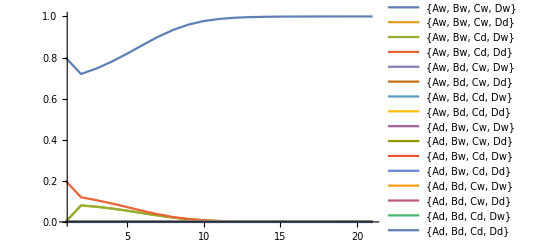

```mathematica
ListLinePlot[Transpose[Table[F2[t],{t,0,20}]],PlotRange->{{1,Automatic},{0,1}},
PlotLegends->Table[ToString[Gametes[[i]]],{i,1,Length[Gametes]}]]
```

## TestCase 2 w/Dominance in EUD

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeFitnessMatrix[{"Ad","Bd"},pars,0.1];
FitnessEUD=MakeDominantPayloadMatrix[{"Cd","Dd"},pars,0.1];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Cd","Dd"},pars,1];
Fitness=FitnessEUD*FitnessPayload*FitnessToxin;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Bd","Dw"},{"Bd","Cw"}},pars,1];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->1/2|>;
```

```mathematica
Clear[F];
F[0]={0.9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.1};
F[t_]:=F[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars],pars]
```

```mathematica
Clear[F2];
F2[0]={0.975,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.025};
F2[t_]:=F2[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F2[t-1],pars],pars],pars],pars]
```

```mathematica
plot2=ListLinePlot[Transpose[Table[F2[t],{t,0,70}]][[{1,4},;;]],PlotStyle->{{ColorData[97,"ColorList"][[1]],Thickness[0.01]},{Dashing[Large],Thickness[0.01],ColorData[97,"ColorList"][[1]]}}];
plot1=ListLinePlot[Transpose[Table[F[t],{t,0,70}]][[{1,4},;;]],PlotRange->{Automatic,{0,1.01}},PlotStyle->{{ColorData[97,"ColorList"][[2]],Thickness[0.01]},{Dashing[Large],Thickness[0.01],ColorData[97,"ColorList"][[2]]}}];
```

```mathematica
load1=ListLinePlot[Table[1-ConvertToGenotypes[F[t],pars].Fitness,{t,0,70}],PlotRange->{Automatic,{0,0.3}},AxesLabel->{"t","Load"},PlotStyle->{Black,Thickness[0.01]}];
load2=ListLinePlot[Table[1-ConvertToGenotypes[F2[t],pars].Fitness,{t,0,70}],PlotRange->{Automatic,{0,0.3}},PlotStyle->{Dashing[Large],Black,Thickness[0.01]}];
```

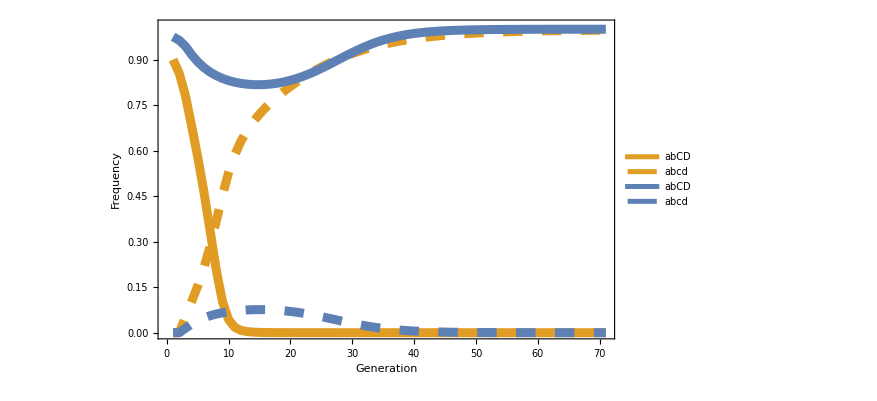

```mathematica
showdyn=Legended[Show[plot1,plot2,
Frame->True, 
FrameLabel->{Style["Generation ",LabelSize],Style["Frequency",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False],
Placed[
LineLegend[{
Directive[Darker[Black],Thickness[0.02],ColorData[97,"ColorList"][[2]]],
Directive[Darker[Black],Thickness[0.02],ColorData[97,"ColorList"][[2]],Dashing[Large],CapForm["Round"]],
Directive[Darker[Black],Thickness[0.02],ColorData[97,"ColorList"][[1]]],
Directive[Darker[Black],Thickness[0.02],ColorData[97,"ColorList"][[1]],Dashing[Large],CapForm["Round"]]
},
{
Style["abCD",LabelSize],
Style["abcd",LabelSize],
Style["abCD",LabelSize],
Style["abcd",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.8,0.3}
]
]
```

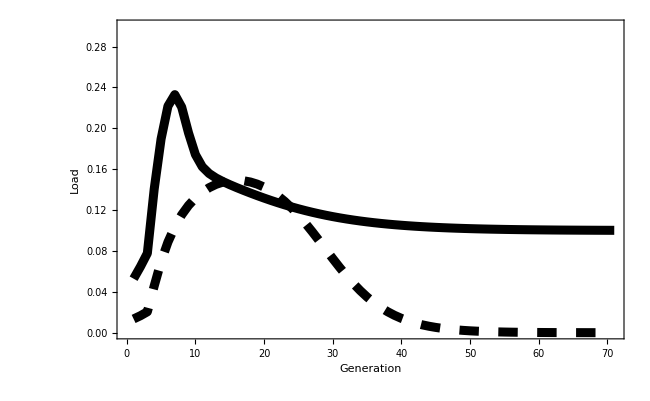

```mathematica
showload=Show[load1,load2,
Frame->True, 
FrameLabel->{Style["Generation ",LabelSize],Style["Load",LabelSize]},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangeClipping->False]
```

## TestCase 2a - Migration

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeFitnessMatrix[{"Ad","Bd"},pars,0.1];
FitnessEUD=MakeDominantPayloadMatrix[{"Cd","Dd"},pars,0.1];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Cd","Dd"},pars,1];
Fitness=FitnessPayload*FitnessToxin;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Bd","Dw"},{"Bd","Cw"}},pars,1];
pars1=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->1/2|>;
```

```mathematica
Clear[F11,F21,F31];
F11[0]={0.9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.1};
F21[0]={1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
F31[0]={1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

m=0.001;
F11[t_]:=F11[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F11[t-1],pars1],pars1],pars1],pars1]
F21[t_]:=F21[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F21[t-1]-m(F21[t-1]-F11[t-1]),pars1],pars1],pars1],pars1]
F31[t_]:=F31[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F31[t-1]-m(F31[t-1]-F21[t-1]),pars1],pars1],pars1],pars1]
```

```mathematica
P11=ListLinePlot[Transpose[Table[F11[t],{t,0,100}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
P21=ListLinePlot[Transpose[Table[F21[t],{t,0,100}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
P31=ListLinePlot[Transpose[Table[F31[t],{t,0,100}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
```

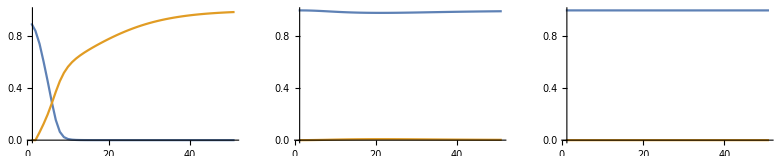

```mathematica
GraphicsGrid[{{P11,P21,P31}}]
```

```mathematica
Clear[F12,F22,F32];
F12[0]={0.9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.1};
F22[0]={1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
F32[0]={1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

m=0.005;
F12[t_]:=F12[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F12[t-1],pars1],pars1],pars1],pars1]
F22[t_]:=F22[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F22[t-1]-m(F22[t-1]-F12[t-1]),pars1],pars1],pars1],pars1]
F32[t_]:=F32[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F32[t-1]-m(F32[t-1]-F22[t-1]),pars1],pars1],pars1],pars1]
```

```mathematica
P12=ListLinePlot[Transpose[Table[F12[t],{t,0,100}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
P22=ListLinePlot[Transpose[Table[F22[t],{t,0,100}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
P32=ListLinePlot[Transpose[Table[F32[t],{t,0,100}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
```

```mathematica
Clear[F13,F23,F33];
F13[0]={0.9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.1};
F23[0]={1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
F33[0]={1.0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

m=0.01;
F13[t_]:=F13[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F13[t-1],pars1],pars1],pars1],pars1]
F23[t_]:=F23[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F23[t-1]-m(F23[t-1]-F13[t-1]),pars1],pars1],pars1],pars1]
F33[t_]:=F33[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F33[t-1]-m(F33[t-1]-F23[t-1]),pars1],pars1],pars1],pars1]
```

```mathematica
P13=ListLinePlot[Transpose[Table[F13[t],{t,0,100}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
P23=ListLinePlot[Transpose[Table[F23[t],{t,0,100}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
P33=ListLinePlot[Transpose[Table[F33[t],{t,0,100}]][[{1,4},;;]],PlotRange->{{1,Automatic},{0,1}}];
```

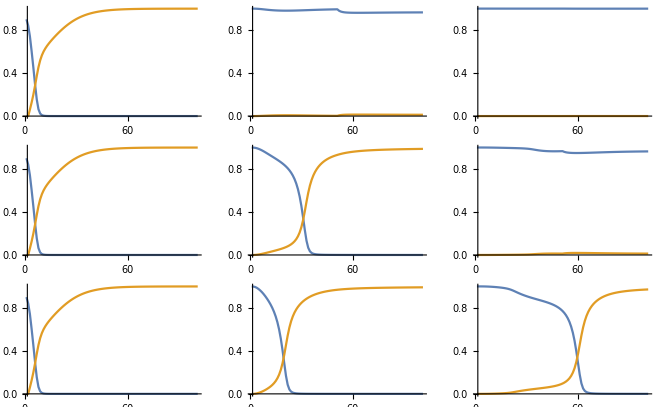

```mathematica
GraphicsGrid[{{P11,P21,P31},{P12,P22,P32},{P13,P23,P33}},PlotLabel->"Dominant payload. m=0.001, m=0.005, m=0.01"]
```

```mathematica
Export["C:\\Users\\Freek\\Documents\\GeneDrive\\Figures\\ExampleMigrationb.pdf",%,"PDF"]
```

C:\Users\Freek\Documents\GeneDrive\Figures\ExampleMigrationb.pdf

## TestCase 3 w/Recessive in EUD

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeFitnessMatrix[{"Ad","Bd"},pars,0.1];
FitnessEUD=MakeRecessivePayloadMatrix[{"Cd","Dd"},pars,0.1];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Cd","Dd"},pars,1];
Fitness=FitnessEUD*FitnessPayload*FitnessToxin;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Bd","Dw"},{"Bd","Cw"}},pars,1];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->1/2|>;
```

```mathematica
Clear[F];
F[0]={0.93,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.07};
F[t_]:=F[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars],pars]
```

```mathematica
plot1=ListLinePlot[Transpose[Table[F[t],{t,0,100}]][[{1,4},;;]],PlotRange->{Automatic,{0,1.01}},AxesLabel->{"t","Freq"}];
```

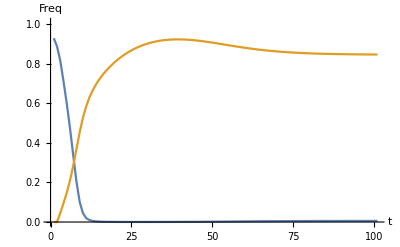

```mathematica
plot1
```

```mathematica
Clear[F2];
F2[0]={0.99,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.01};
F2[t_]:=F2[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F2[t-1],pars],pars],pars],pars]
```

```mathematica
plot2=ListLinePlot[Transpose[Table[F2[t],{t,0,100}]][[{1,4},;;]],PlotStyle->Dashed];
```

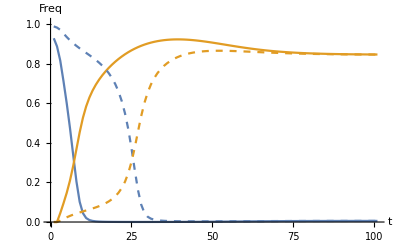

```mathematica
showdyn=Show[plot1,plot2]
```

```mathematica
load1=ListLinePlot[Table[1-ConvertToGenotypes[F[t],pars].Fitness,{t,0,100}],PlotRange->{Automatic,{0,0.5}},AxesLabel->{"t","Load"},PlotStyle->Black];
load2=ListLinePlot[Table[1-ConvertToGenotypes[F2[t],pars].Fitness,{t,0,100}],PlotRange->{Automatic,{0,1}},PlotStyle->{Dashed,Black}];
```

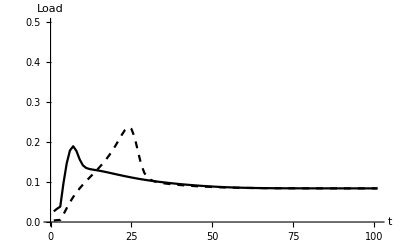

```mathematica
showload=Show[load1,load2]
```

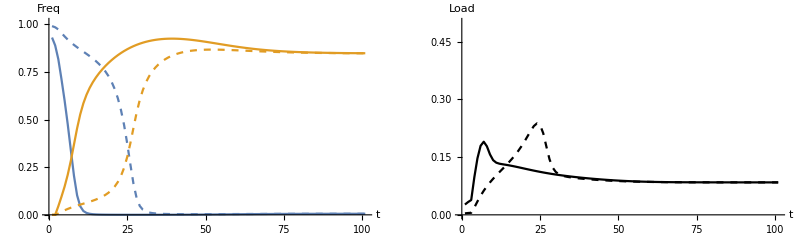

```mathematica
GraphicsGrid[{{showdyn,showload}},PlotLabel->"Recessive payload, 4Loci, s=0.1,d=1,ϵ=1,r=0.5"]
```

```mathematica
Export["C:\\Users\\Freek\\Documents\\GeneDrive\\Figures\\Example4Loci1.pdf",%959,"PDF"]
```

C:\Users\Freek\Documents\GeneDrive\Figures\Example4Loci1.pdf

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;

FitnessPayload=MakeFitnessMatrix[{"Ad","Bd"},pars,0.1];
FitnessEUD=MakeDominantPayloadMatrix[{"Cd","Dd"},pars,0.1];
FitnessToxin=Make2LocusUnderDominanceFitnessMatrix[{"Cd","Dd"},pars,1];
Fitness=FitnessEUD*FitnessPayload*FitnessToxin;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Bd","Dw"},{"Bd","Cw"}},pars,1];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"Fitness"->Fitness,"DriveMatrix"->DriveMatrix,"recombination"->1/2|>;
```

```mathematica
Clear[F];
F[0]={0.9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.1};
F[t_]:=F[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F[t-1],pars],pars],pars],pars]
```

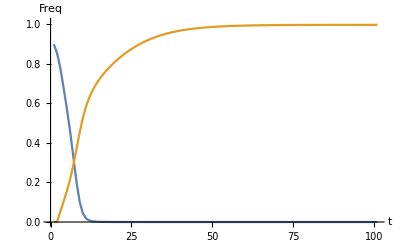

```mathematica
plot1=ListLinePlot[Transpose[Table[F[t],{t,0,100}]][[{1,4},;;]],PlotRange->{Automatic,{0,1.01}},AxesLabel->{"t","Freq"}]
```

```mathematica
Clear[F2];
F2[0]={0.975,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.025};
F2[t_]:=F2[t]=Recombination[Drive[DiploidSelection[ConvertToGenotypes[F2[t-1],pars],pars],pars],pars]
```

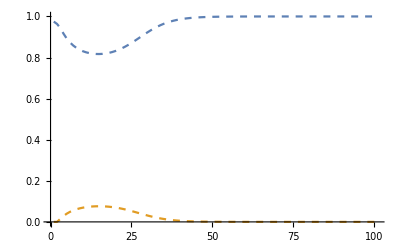

```mathematica
plot2=ListLinePlot[Transpose[Table[F2[t],{t,0,100}]][[{1,4},;;]],PlotStyle->Dashed]
```

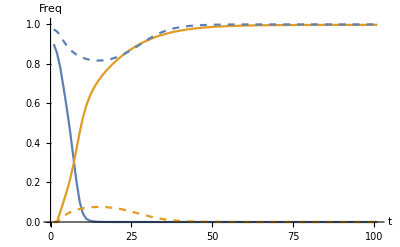

```mathematica
showdyn=Show[plot1,plot2]
```

```mathematica
load1=ListLinePlot[Table[1-ConvertToGenotypes[F[t],pars].Fitness,{t,0,100}],PlotRange->{Automatic,{0,0.5}},AxesLabel->{"t","Load"},PlotStyle->Black];
load2=ListLinePlot[Table[1-ConvertToGenotypes[F2[t],pars].Fitness,{t,0,100}],PlotRange->{Automatic,{0,1}},PlotStyle->{Dashed,Black}];
```

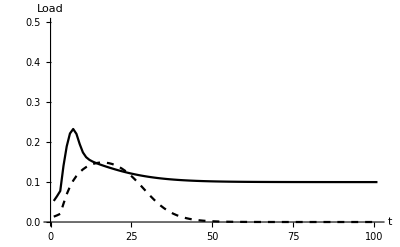

```mathematica
showload=Show[load1,load2]
```

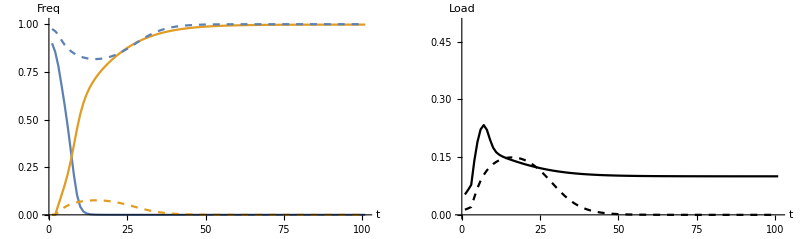

```mathematica
GraphicsGrid[{{showdyn,showload}},PlotLabel->"Dominant payload, 4Loci, s=0.1,d=1,ϵ=1,r=0.5"]
```

# Point of focus: check dynamics of initializer of daisy chain and its interaction with migration. Maybe analytical work to show weather or not invasion will occur.

```mathematica
Loci={{"Aw","Ad"},{"Bw","Bd"},{"Cw","Cd"},{"Dw","Dd"}};
Gametes =Tuples[Loci];
Genotypes=Tuples[Gametes,2];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes|>;
(*ArrayReshape[Fitness,{Length[Gametes],Length[Gametes]}]//MatrixForm;*)
DriveMatrix=MakeDriveMatrix[{{"Ad","Bw"},{"Bd","Dw"},{"Bd","Cw"}},pars,d];
pars=<|"Loci"->Loci,"Gametes"->Gametes,"Genotypes"->Genotypes,"DriveMatrix"->DriveMatrix,"recombination"->r|>;
```

```mathematica
Clear[F];
nextgen=ConvertToGenotypes[Recombination[Drive[Table[F[i],{i,1,Length[Genotypes]}],pars],pars],pars]
```

{((1-r)^3 F[1]+3 (1-r)^2 r F[1]+3 (1-r) r^2 F[1]+r^3 F[1]+1/2 (1-r)^3 F[2]+3/2 (1-r)^2 r F[2]+3/2 (1-r) r^2 F[2]+1/2 r^3 F[2]+1/2 (1-r)^3 F[3]+158+1/2 (1-d)^2 (1-r) r^2 F[195]+1/2 (1-d)^3 (1-r)^2 r F[196]+1/2 (1-d)^2 (1-r)^3 F[209]+1/2 (1-d)^2 (1-r) r^2 F[209]+1/2 (1-d)^3 (1-r) r^2 F[211]+1/2 (1-d)^2 (1-r)^3 F[225]+1/2 (1-d)^2 (1-r)^2 r F[225]+1/2 (1-d)^3 (1-r)^2 r F[226]+1/2 (1-d)^3 (1-r)^3 F[241])^2,((1-r)^3 F[1]+3 (1-r)^2 r F[1]+3 (1-r) r^2 F[1]+r^3 F[1]+1/2 (1-r)^3 F[2]+166+1/2 (1-d)^3 (1-r) r^2 F[211]+1/2 (1-d)^2 (1-r)^3 F[225]+1/2 (1-d)^2 (1-r)^2 r F[225]+1/2 (1-d)^3 (1-r)^2 r F[226]+1/2 (1-d)^3 (1-r)^3 F[241]) (1),252,(1) 1,(1/2 (1-d)^3 (1-r)^3 F[16]+174+r^3 (d^3 F[144]+d^3 F[159]+d^2 F[160]+d^3 F[174]+d^2 F[176]+d^3 F[189]+d^2 F[190]+d^2 F[191]+12+d^2 F[250]+d^2 F[251]+d F[252]+d^2 F[253]+d F[254]+d F[255]+F[256]))^2}
 |  |  |  |

```mathematica
Length[Genotypes]
```

256

```mathematica
nextgen[[1]]
```

(((1-r)^3 F[1]+3 (1-r)^2 r F[1]+3 (1-r) r^2 F[1]+r^3 F[1]+1/2 (1-r)^3 F[2]+3/2 (1-r)^2 r F[2]+3/2 (1-r) r^2 F[2]+1/2 r^3 F[2]+1/2 (1-r)^3 F[3]+3/2 (1-r)^2 r F[3]+3/2 (1-r) r^2 F[3]+1/2 r^3 F[3]+1/2 (1-r)^3 F[4]+(1-r)^2 r F[4]+1/2 (1-r) r^2 F[4]+1/2 (1-r)^3 F[5]+3/2 (1-r)^2 r F[5]+3/2 (1-r) r^2 F[5]+1/2 r^3 F[5]+1/2 (1-d) (1-r)^3 F[6]+1/2 (1-d) (1-r)^2 r F[6]+1/2 (1-d) (1-r) r^2 F[6]+1/2 (1-d) r^3 F[6]+1/2 (1-d) (1-r)^3 F[7]+(1-d) (1-r)^2 r F[7]+1/2 (1-d) (1-r) r^2 F[7]+1/2 (1-d)^2 (1-r)^3 F[8]+1/2 (1-d)^2 (1-r)^2 r F[8]+1/2 (1-r)^3 F[9]+3/2 (1-r)^2 r F[9]+3/2 (1-r) r^2 F[9]+1/2 r^3 F[9]+1/2 (1-r)^3 F[10]+3/2 (1-r) r^2 F[10]+1/2 (1-r)^3 F[11]+1/2 (1-r)^2 r F[11]+1/2 (1-r) r^2 F[11]+1/2 r^3 F[11]+1/2 (1-r)^3 F[12]+1/2 (1-r) r^2 F[12]+1/2 (1-d) (1-r)^3 F[13]+(1-d) (1-r)^2 r F[13]+1/2 (1-d) (1-r) r^2 F[13]+1/2 (1-d)^2 (1-r)^3 F[14]+1/2 (1-d)^2 (1-r) r^2 F[14]+1/2 (1-d)^2 (1-r)^3 F[15]+1/2 (1-d)^2 (1-r)^2 r F[15]+1/2 (1-d)^3 (1-r)^3 F[16]+1/2 (1-r)^3 F[17]+3/2 (1-r)^2 r F[17]+3/2 (1-r) r^2 F[17]+1/2 r^3 F[17]+1/2 (1-r)^2 r F[19]+(1-r) r^2 F[19]+1/2 r^3 F[19]+(1-d) (1-r)^2 r F[21]+(1-d) (1-r) r^2 F[21]+1/2 (1-d)^2 (1-r)^2 r F[23]+1/2 (1-d)^2 (1-r) r^2 F[23]+3/2 (1-r)^2 r F[25]+1/2 r^3 F[25]+1/2 (1-r)^2 r F[27]+1/2 r^3 F[27]+(1-d)^2 (1-r)^2 r F[29]+1/2 (1-d)^3 (1-r)^2 r F[31]+1/2 (1-r)^3 F[33]+3/2 (1-r)^2 r F[33]+3/2 (1-r) r^2 F[33]+1/2 r^3 F[33]+1/2 (1-r)^2 r F[34]+(1-r) r^2 F[34]+1/2 r^3 F[34]+1/2 (1-d) (1-r)^2 r F[37]+(1-d) (1-r) r^2 F[37]+1/2 (1-d) r^3 F[37]+1/2 (1-d)^2 (1-r) r^2 F[38]+1/2 (1-d)^2 r^3 F[38]+(1-r)^2 r F[41]+(1-r) r^2 F[41]+(1-r) r^2 F[42]+1/2 (1-d)^2 (1-r)^2 r F[45]+1/2 (1-d)^2 (1-r) r^2 F[45]+1/2 (1-d)^3 (1-r) r^2 F[46]+1/2 (1-r)^3 F[49]+(1-r)^2 r F[49]+1/2 (1-r) r^2 F[49]+1/2 (1-d)^2 (1-r)^2 r F[53]+1/2 (1-d)^2 (1-r) r^2 F[53]+(1-r)^2 r F[57]+1/2 (1-d)^3 (1-r)^2 r F[61]+1/2 (1-r)^3 F[65]+3/2 (1-r)^2 r F[65]+3/2 (1-r) r^2 F[65]+1/2 r^3 F[65]+(1-d) (1-r)^2 r F[66]+(1-d) (1-r) r^2 F[66]+1/2 (1-d) (1-r)^2 r F[67]+(1-d) (1-r) r^2 F[67]+1/2 (1-d) r^3 F[67]+1/2 (1-d)^2 (1-r)^2 r F[68]+1/2 (1-d)^2 (1-r) r^2 F[68]+1/2 (1-d) (1-r)^2 r F[73]+(1-d) (1-r) r^2 F[73]+1/2 (1-d) r^3 F[73]+(1-d)^2 (1-r) r^2 F[74]+1/2 (1-d)^2 (1-r) r^2 F[75]+1/2 (1-d)^2 r^3 F[75]+1/2 (1-d)^3 (1-r) r^2 F[76]+1/2 (1-d) (1-r)^3 F[81]+1/2 (1-d) (1-r)^2 r F[81]+1/2 (1-d) (1-r) r^2 F[81]+1/2 (1-d) r^3 F[81]+1/2 (1-d)^2 (1-r) r^2 F[83]+1/2 (1-d)^2 r^3 F[83]+1/2 (1-d)^2 (1-r)^2 r F[89]+1/2 (1-d)^2 r^3 F[89]+1/2 (1-d)^3 r^3 F[91]+1/2 (1-d) (1-r)^3 F[97]+(1-d) (1-r)^2 r F[97]+1/2 (1-d) (1-r) r^2 F[97]+1/2 (1-d)^2 (1-r)^2 r F[98]+1/2 (1-d)^2 (1-r) r^2 F[98]+1/2 (1-d)^2 (1-r)^2 r F[105]+1/2 (1-d)^2 (1-r) r^2 F[105]+1/2 (1-d)^3 (1-r) r^2 F[106]+1/2 (1-d)^2 (1-r)^3 F[113]+1/2 (1-d)^2 (1-r)^2 r F[113]+1/2 (1-d)^3 (1-r)^2 r F[121]+1/2 (1-r)^3 F[129]+3/2 (1-r)^2 r F[129]+3/2 (1-r) r^2 F[129]+1/2 r^3 F[129]+3/2 (1-r)^2 r F[130]+1/2 r^3 F[130]+(1-r)^2 r F[131]+(1-r) r^2 F[131]+(1-r)^2 r F[132]+1/2 (1-d) (1-r)^2 r F[133]+(1-d) (1-r) r^2 F[133]+1/2 (1-d) r^3 F[133]+1/2 (1-d)^2 (1-r)^2 r F[134]+1/2 (1-d)^2 r^3 F[134]+1/2 (1-d)^2 (1-r)^2 r F[135]+1/2 (1-d)^2 (1-r) r^2 F[135]+1/2 (1-d)^3 (1-r)^2 r F[136]+1/2 (1-r)^3 F[145]+3/2 (1-r) r^2 F[145]+(1-r) r^2 F[147]+(1-d)^2 (1-r) r^2 F[149]+1/2 (1-d)^3 (1-r) r^2 F[151]+1/2 (1-r)^3 F[161]+1/2 (1-r)^2 r F[161]+1/2 (1-r) r^2 F[161]+1/2 r^3 F[161]+1/2 (1-r)^2 r F[162]+1/2 r^3 F[162]+1/2 (1-d)^2 (1-r) r^2 F[165]+1/2 (1-d)^2 r^3 F[165]+1/2 (1-d)^3 r^3 F[166]+1/2 (1-r)^3 F[177]+1/2 (1-r) r^2 F[177]+1/2 (1-d)^3 (1-r) r^2 F[181]+1/2 (1-d) (1-r)^3 F[193]+(1-d) (1-r)^2 r F[193]+1/2 (1-d) (1-r) r^2 F[193]+(1-d)^2 (1-r)^2 r F[194]+1/2 (1-d)^2 (1-r)^2 r F[195]+1/2 (1-d)^2 (1-r) r^2 F[195]+1/2 (1-d)^3 (1-r)^2 r F[196]+1/2 (1-d)^2 (1-r)^3 F[209]+1/2 (1-d)^2 (1-r) r^2 F[209]+1/2 (1-d)^3 (1-r) r^2 F[211]+1/2 (1-d)^2 (1-r)^3 F[225]+1/2 (1-d)^2 (1-r)^2 r F[225]+1/2 (1-d)^3 (1-r)^2 r F[226]+1/2 (1-d)^3 (1-r)^3 F[241]))^2